# collection of Gaussian beam through hole

How much power is transmitted through the hole if the beam is focused z away (well outside the Rayleigh range)

```mathematica
z=5;
λ=8.5*10^-4;
w0 = 0.5*10^-3;
η=0.05;
(z λ)/(π w0)√η
```

0.604998

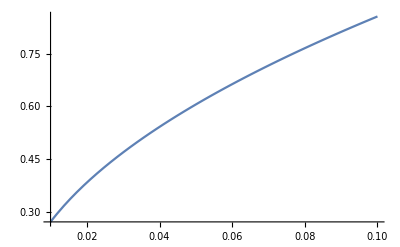

```mathematica
Plot[(z λ)/(π w0)√eta,{eta,0.01,0.1}]
```

How much light from a fixed NA source through a hole?

```mathematica
θ=ArcSin[NA]/.NA->0.6;
(*emission surface*)
Integrate[Sin[th],{th,0,2θ},{ph,0,2θ}] r^2
```

0.926642 r^2

```mathematica
(*check against spherical shell area*)
0.9266415966623295 /(4π)
```

0.0737398

```mathematica
(λ f)/(w1 π)
```

```mathematica
((8.5*^-4)*5.25)/(3.9π)
```

0.00036422